```mathematica
data=Import["pressfull1.tsv"]
data2 = Import["1397002.csv"]
```

{{timecode,yday,degC,Pa,pressAltComp},{1529815303,174,21.9,101124,16.9978},{1529815803,174,22.,101137,15.9972},{1529816303,174,21.9,101137,16.1639},{1529816803,174,21.9,101125,15.6636},{1529817303,174,21.9,101120,17.7483},{1529817803,174,21.8,101111,17.8317},{1529818303,174,21.8,101106,18.0819},{1529818803,174,21.8,101109,18.5823},{1529819303,174,21.8,101104,18.0819},{1529819803,174,21.9,101092,18.4155},{1529820303,174,21.8,101099,19.0828},{1529820803,174,21.8,101087,19.8335},{1529821303,174,21.8,101077,20.5008},{1529821803,174,21.7,101084,20.334},{1529822303,174,22.,101088,19.5832},{1529822803,174,22.4,101079,20.7511},{1529915775,175,21.9,100440,74.0261},{1529916275,175,21.9,100440,74.2777},{1529916775,175,21.9,100429,74.8646},{1529917275,175,21.8,100432,74.6131},{1529917775,175,21.8,100414,75.3678},{1529918275,175,21.8,100414,75.6194},{1529918775,175,21.7,100426,75.0324},{1529919275,175,21.6,100440,74.4454},{1529919775,175,21.6,100430,75.1162},{1529920275,175,21.5,100436,74.4454},{1529920775,175,21.4,100437,75.2839},{1529921275,175,21.3,100425,74.6969},{1529921775,175,21.3,100438,73.8584},{1529922275,175,21.2,100451,73.2715},{1529922775,175,21.1,100460,71.8463},{1529923275,175,21.1,100484,70.2536},{1529923775,175,21.,100493,69.6669},{1529924275,175,21.,100497,69.2478},{1529924775,175,20.9,100510,68.5774},{1529925275,175,20.9,100493,69.0802},{1529925775,175,20.9,100490,69.4155},{1529926275,175,20.8,100500,68.9126},{1529926775,175,20.7,100505,69.0802},{1529927275,175,20.7,100512,67.1528},{1529927775,175,20.7,100522,67.3204},{1529928275,175,20.6,100532,66.5663},{1529928775,175,20.6,100532,65.4771},{1529929275,175,20.6,100538,65.7284},{1529929775,175,20.5,100544,65.0582},{1529930275,175,20.4,100551,64.8068},{1529930775,175,20.4,100559,64.3042},{1529931275,175,20.3,100552,64.2204},{1529931775,175,20.3,100555,64.5555},{1529932275,175,20.3,100575,62.7964},{1529932775,175,20.2,100588,62.0426},{1529933275,175,20.2,100592,61.4564},{1529933775,175,20.2,100592,60.8702},{1529934275,175,20.1,100605,59.7816},{1529934775,175,20.1,100612,59.3629},{1529935275,175,20.1,100629,58.4419},{1529935775,175,20.,100625,57.2699},{1529936275,175,19.9,100638,58.0233},{1529936775,175,19.9,100647,56.3491},{1529937275,175,19.9,100665,55.8468},{1529937775,175,19.9,100676,55.3446},{1529938275,175,19.8,100676,53.9218},{1529938775,175,19.8,100690,52.4993},{1529939275,175,19.8,100696,51.4115},{1529939775,175,19.8,100716,50.9096},{1529940275,175,19.8,100722,49.6547},{1529940775,175,19.8,100740,48.6509},{1529941275,175,19.9,100742,47.5636},{1529941775,175,19.9,100759,47.229},{1529942275,175,20.,100773,46.4764},{1529942775,175,20.,100789,45.222},{1529943275,175,20.,100795,44.1351},{1530345415,180,21.8,101208,8.99538},{1530345914,180,21.7,101197,10.2454},{1530346414,180,21.7,101205,9.82868},{1530346914,180,22.,101210,9.66202},{1530347414,180,21.9,101196,10.662},{1530347914,180,21.7,101197,9.82868},{1530348414,180,21.7,101211,9.49535},{1530348914,180,21.7,101218,8.99538},{1530349414,180,21.6,101208,8.91206},{1530349914,180,21.6,101196,11.7455},{1530350414,180,21.6,101195,10.7454},{1530350914,180,21.5,101193,9.99535},{1530351414,180,21.5,101208,9.74535},{1530351914,180,21.5,101193,11.0788},{1530352414,180,21.5,101188,12.9958},{1530352914,180,21.4,101190,10.5787},{1530353414,180,21.4,101192,11.4955},{1530353914,180,21.3,101179,11.3288},{1530354414,180,21.3,101193,10.4954},{1530354914,180,21.3,101193,10.7454},{1530355414,180,21.3,101186,10.9121},{1530355914,180,21.3,101200,10.412},{1530356414,180,21.2,101217,8.91206},{1530356914,180,21.2,101220,8.91206},{1530357414,180,21.2,101215,8.07883},{1530357914,180,21.2,101218,8.99538},{1530358414,180,21.1,101227,8.16215},{1530358914,180,21.1,101231,8.32879},{1530359414,180,21.1,101234,7.99551},{1530359914,180,21.1,101240,6.99574},{1530360414,180,21.,101258,5.24636},{1530360914,180,21.,101252,6.16267},{1530361414,180,21.,101258,5.99606},{1530361914,180,21.,101266,4.6633},{1530362414,180,21.,101253,6.6625},{1530362914,180,20.9,101266,4.6633},{1530363414,180,20.9,101283,3.83042},{1530363914,180,20.9,101283,3.33072},{1530364414,180,20.9,101300,2.49794},{1530364914,180,20.9,101299,2.16485},{1530365414,180,20.9,101300,2.66449},{1530365914,180,20.8,101294,2.58121},{1530366414,180,20.9,101297,2.58121},{1530366914,180,20.8,101273,4.6633},{1530367414,180,20.8,101287,3.74713},{1530367914,180,20.8,101287,3.16416},{1530368414,180,20.8,101308,1.74849},{1530368914,180,20.8,101318,0.49954},{1530369414,180,20.8,101308,1.9983},{1530369914,180,20.8,101301,1.83176},{1530370414,180,20.8,101296,1.08237},{1530370914,180,20.7,101304,0.999103},{1530371414,180,20.7,101322,0.},{1530371914,180,20.7,101327,-0.999008},{1530372414,180,20.7,101335,-0.999008},{1530372914,180,20.7,101314,0.915841},{1530373414,180,20.7,101309,1.33216},{1530373914,180,20.7,101332,-0.666016},{1530374414,180,20.7,101332,-1.49848},{1530374914,180,20.7,101330,-0.333013},{1530375414,180,20.7,101330,-1.1655},{1530375914,180,20.7,101326,0.249767},{1530376414,180,20.7,101343,-0.999008},{1530376914,180,20.7,101323,-0.166508},{1530377414,180,20.8,101326,-0.0832543},{1530377914,180,20.8,101333,0.249767},{1530378414,180,20.9,101309,0.999103},{1530378914,180,20.9,101312,1.33216},{1530379414,180,21.,101314,0.416281},{1530379914,180,21.1,101318,0.416281},{1530380414,180,21.,101324,0.416281},{1530380914,180,21.1,101313,1.58196},{1530381414,180,21.1,101313,1.41542},{1530381914,180,21.1,101294,1.74849},{1530382414,180,21.2,101304,1.83176},{1530382914,180,21.2,101306,1.33216},{1530383414,180,21.2,101315,1.33216},{1530383914,180,21.3,101307,1.24889},{1530384414,180,21.3,101307,0.749319},{1530384914,180,21.2,101310,0.999103},{1530385414,180,21.2,101306,1.49869},{1530385914,180,21.2,101315,0.999103},{1530386414,180,21.2,101307,1.24889},{1530386914,180,21.3,101309,1.33216},{1530387414,180,21.3,101306,1.08237},{1530387914,180,21.3,101312,0.249767},{1530388414,180,21.2,101315,0.666058},{1530388914,180,21.3,101316,0.749319},{1530389414,180,21.3,101291,2.41466},{1530389914,180,21.3,101293,2.41466},{1530390414,180,21.2,101296,2.16485},{1530390914,180,21.3,101310,1.58196},{1530391414,180,21.3,101300,2.83104},{1530391914,180,21.3,101310,1.58196},{1530392414,180,21.3,101306,0.999103},{1530392914,180,21.3,101311,1.58196},{1530393414,180,21.3,101301,1.58196},{1530393914,180,21.3,101289,2.41466},{1530394414,180,21.4,101268,4.91318},{1530394914,180,21.5,101251,6.57919},{1530395414,180,21.5,101275,3.83042},{1530395914,180,21.5,101276,3.66385},{1530396414,180,21.5,101265,4.7466},{1530396914,180,21.5,101281,3.49728},{1530397414,180,21.5,101281,4.16356},{1530397914,180,21.5,101279,3.414},{1530398414,180,21.5,101285,3.58056},{1530398914,180,21.6,101261,5.24636},{1530399414,180,21.6,101264,5.24636},{1530399914,180,21.6,101248,5.66285},{1530400414,180,21.6,101247,6.32927},{1530400914,180,21.7,101241,6.41258},{1530401414,180,21.7,101248,5.74615},{1530401914,180,21.8,101244,6.99574},{1530402414,180,21.8,101239,7.32898},{1530402914,180,21.8,101234,7.32898},{1530403414,181,21.9,101227,8.41211},{1530403914,181,22.,101220,7.74556},{1530404414,181,22.1,101214,8.82873},{1530404914,181,22.2,101222,8.99538},{1530405414,181,22.2,101215,8.16215},{1530405914,181,22.2,101201,9.49535},{1530406414,181,22.3,101200,10.2454},{1530406914,181,22.3,101191,10.8287},{1530407414,181,22.3,101194,11.2454},{1530407914,181,22.3,101188,10.9954},{1530408414,181,22.3,101193,11.6622},{1530408914,181,22.3,101200,9.74535},{1530409414,181,22.4,101210,10.0787},{1530409914,181,22.4,101206,10.162},{1530410414,181,22.4,101201,10.4954},{1530410914,181,22.4,101196,10.9121},{1530411414,181,22.4,101191,10.4954},{1530411914,181,22.4,101196,11.4955},{1530412414,181,22.4,101192,10.4954},{1530412914,181,22.5,101197,10.9121},{1530413414,181,22.4,101203,10.2454},{1530413914,181,22.4,101200,10.662},{1530414414,181,22.5,101204,10.0787},{1530414914,181,22.5,101215,9.32869},{1530415414,181,22.5,101209,9.66202},{1530415914,181,22.5,101205,10.4954},{1530416414,181,22.5,101205,9.91202},{1530416914,181,22.5,101207,10.412},{1530417414,181,22.5,101214,10.0787},{1530417914,181,22.4,101212,10.0787},{1530418414,181,22.4,101204,10.0787},{1530418914,181,22.4,101209,9.66202},{1530419414,181,22.4,101219,9.57868},{1530419914,181,22.4,101216,8.66208},{1530420414,181,22.3,101214,8.24547},{1530420914,181,22.3,101227,8.24547},{1530421414,181,22.3,101230,8.41211},{1530421914,181,22.3,101243,7.07905},{1530422414,181,22.3,101250,7.24567},{1530422914,181,22.2,101237,6.82912},{1530423414,181,22.2,101240,7.57893},{1530423914,181,22.2,101235,7.57893},{1530424414,181,22.2,101225,7.91219},{1530424914,181,22.2,101234,7.82888},{1530425414,181,22.2,101248,6.74581},{1530425914,181,22.2,101239,7.24567},{1530426414,181,22.2,101234,7.57893},{1530426914,181,22.2,101234,7.49561},{1530427414,181,22.2,101245,6.41258},{1530427914,181,22.1,101248,7.16236},{1530428414,181,22.1,101236,6.6625},{1530428914,181,22.1,101234,7.24567},{1530429414,181,22.1,101242,6.74581},{1530429914,181,22.1,101239,6.99574},{1530430414,181,22.1,101245,6.41258},{1530430914,181,22.,101235,6.99574},{1530431414,181,22.,101232,7.4123},{1530431914,181,22.,101239,7.16236},{1530432414,181,22.,101249,6.91243},{1530432914,181,22.,101248,6.16267},{1530433414,181,22.,101255,5.82945},{1530433914,181,22.,101243,6.91243},{1530434414,181,22.,101252,5.99606},{1530434914,181,21.9,101252,6.32927},{1530435414,181,21.9,101253,6.24597},{1530435914,181,21.9,101256,5.99606},{1530436414,181,21.9,101240,6.6625},{1530436914,181,21.9,101236,7.4123},{1530437414,181,21.8,101231,7.32898},{1530437914,181,21.8,101239,7.66224},{1530438414,181,21.9,101236,7.4123},{1530438914,181,21.8,101231,8.16215},{1530439414,181,21.8,101226,7.91219},{1530439914,181,21.8,101227,7.82888},{1530440414,181,21.8,101231,7.91219},{1530440914,181,21.8,101241,7.07905},{1530441414,181,21.8,101234,7.82888},{1530441914,181,21.8,101231,7.82888},{1530442414,181,21.8,101237,7.57893},{1530442914,181,21.7,101244,7.07905},{1530443414,181,21.7,101235,6.49589},{1530443914,181,21.7,101240,5.82945},{1530444414,181,21.7,101245,6.74581},{1530444914,181,21.7,101230,7.07905},{1530445414,181,21.7,101232,7.24567},{1530445914,181,21.7,101235,6.99574},{1530446414,181,21.6,101234,7.99551},{1530446914,181,21.6,101237,7.16236},{1530447414,181,21.6,101239,7.32898},{1530447914,181,21.6,101245,6.6625},{1530448414,181,21.6,101252,5.91276},{1530448914,181,21.5,101248,5.91276},{1530449414,181,21.5,101262,5.32966},{1530449914,181,21.5,101272,4.99648},{1530450414,181,21.5,101275,4.24685},{1530450914,181,21.5,101286,3.9137},{1530451414,181,21.5,101293,2.24812},{1530451914,181,21.5,101293,1.83176},{1530452414,181,21.5,101295,1.83176},{1530452914,181,21.5,101288,2.9976},{1530453414,181,21.4,101296,2.66449},{1530453914,181,21.4,101296,1.83176},{1530454414,181,21.4,101297,1.91503},{1530454914,181,21.4,101292,2.74777},{1530455414,181,21.3,101306,1.58196},{1530455914,181,21.3,101300,1.16563},{1530456414,181,21.3,101320,0.166511},{1530456914,181,21.3,101328,-0.333013},{1530457414,181,21.3,101335,-0.416265},{1530457914,181,21.3,101326,0.},{1530458414,181,21.3,101322,-0.0832543},{1530458914,181,21.2,101322,-0.0832543},{1530459414,181,21.3,101327,-0.582766},{1530459914,181,21.2,101333,-0.832513},{1530460414,181,21.2,101345,-1.83144},{1530460914,181,21.2,101339,-1.99792},{1530461414,181,21.2,101346,-2.08116},{1530461914,181,21.3,101357,-2.9135},{1530462414,181,21.3,101350,-2.49734},{1530462914,181,21.3,101358,-2.66381},{1530463414,181,21.3,101367,-3.82901},{1530463914,181,21.3,101371,-3.74578},{1530464414,181,21.3,101374,-4.32834},{1530464914,181,21.3,101360,-2.24763},{1530465414,181,21.3,101358,-2.1644},{1530465914,181,21.4,101344,-1.91468},{1530466414,181,21.4,101357,-2.24763},{1530466914,181,21.4,101358,-3.41288},{1530467414,181,21.4,101366,-3.41288},{1530467914,181,21.3,101370,-3.99546},{1530468414,181,21.3,101364,-3.24642},{1530468914,181,21.4,101376,-4.07868},{1530469414,181,21.4,101380,-4.578},{1530469914,181,21.3,101381,-4.91087},{1530470414,181,21.4,101374,-4.32834},{1530470914,181,21.3,101383,-5.41015},{1530471414,181,21.3,101380,-4.578},{1530471914,181,21.4,101388,-4.41156},{1530472414,181,21.3,101380,-5.0773},{1530472914,181,21.4,101376,-4.41156},{1530473414,181,21.4,101374,-4.24512},{1530473914,181,21.4,101383,-4.82765},{1530474414,181,21.4,101390,-4.66122},{1530474914,181,21.4,101384,-4.41156},{1530475414,181,21.4,101371,-4.24512},{1530475914,181,21.4,101364,-3.66256},{1530476414,181,21.4,101363,-2.99674},{1530476914,181,21.4,101360,-2.66381},{1530477414,181,21.3,101349,-1.99792},{1530477914,181,21.3,101340,-1.08225},{1530478414,181,21.3,101342,-1.1655},{1530478914,181,21.3,101323,-0.499516},{1530479414,181,21.4,101339,-1.08225},{1530479914,181,21.4,101335,-1.33199},{1530480414,181,21.4,101332,-0.832513},{1530480914,181,21.4,101337,-1.08225},{1530481414,181,21.5,101334,-0.999008},{1530481914,181,21.5,101340,-0.999008},{1530482414,181,21.5,101320,-0.249761},{1530482914,181,21.6,101315,0.416281},{1530483414,181,21.6,101324,0.582799},{1530483914,181,21.6,101333,-0.749265},{1530484414,181,21.6,101330,-0.166508},{1530484914,181,21.6,101333,0.166511},{1530485414,181,21.6,101320,0.333024},{1530485914,181,21.6,101336,-0.749265},{1530486414,181,21.6,101337,-0.749265},{1530486914,181,21.6,101338,-0.915761},{1530487414,181,21.5,101347,-0.749265},{1530487914,181,21.5,101342,-0.832513},{1530488414,181,21.5,101338,-0.749265},{1530488914,181,21.5,101343,-1.41523},{1530489414,181,21.5,101342,-1.58172},{1530489914,182,21.5,101351,-1.91468},{1530490414,182,21.4,101356,-2.1644},{1530490914,182,21.4,101356,-2.1644},{1530491414,182,21.4,101351,-2.74704},{1530491914,182,21.4,101345,-1.7482},{1530492414,182,21.3,101355,-2.24763},{1530492914,182,21.3,101364,-1.7482},{1530493414,182,21.3,101340,-1.49848},{1530493914,182,21.3,101340,-0.832513},{1530494414,182,21.2,101327,-0.0832543},{1530494914,182,21.2,101333,-1.24874},{1530495414,182,21.2,101333,-0.832513},{1530495914,182,21.2,101320,0.},{1530496414,182,21.2,101313,1.33216},{1530496914,182,21.2,101316,0.},{1530497414,182,21.3,101317,-0.249761},{1530497914,182,21.3,101320,-0.249761},{1530498414,182,21.2,101327,0.249767},{1530498914,182,21.3,101325,-0.249761},{1530499414,182,21.2,101333,0.},{1530499914,182,21.2,101332,-0.582766},{1530500414,182,21.2,101339,-0.832513},{1530500914,182,21.3,101332,-0.582766},{1530501414,182,21.3,101332,-0.416265},{1530501914,182,21.3,101336,-0.416265},{1530502414,182,21.3,101329,-0.832513},{1530502914,182,21.3,101332,-0.832513},{1530503414,182,21.3,101333,0.},{1530503914,182,21.3,101323,-0.0832543},{1530504414,182,21.3,101313,0.83258},{1530504914,182,21.3,101318,0.582799},{1530505414,182,21.4,101318,0.749319},{1530505914,182,21.4,101328,-0.249761},{1530506414,182,21.4,101334,-0.749265},{1530506914,182,21.4,101342,-0.999008},{1530507414,182,21.4,101342,-1.08225},{1530507914,182,21.4,101342,-1.83144},{1530508414,182,21.3,101339,-1.41523},{1530508914,182,21.2,101342,-1.66496},{1530509414,182,21.1,101334,-1.1655},{1530509914,182,21.1,101334,-1.24874},{1530510414,182,21.,101330,-0.999008},{1530510914,182,21.,101337,-1.33199},{1530511414,182,21.,101337,-0.499516},{1530511914,182,21.,101321,0.416281},{1530512414,182,21.,101332,-0.166508},{1530512914,182,21.,101330,-0.999008},{1530513414,182,21.,101324,0.},{1530513914,182,21.,101332,-0.416265},{1530514414,182,21.,101331,0.},{1530514914,182,20.9,101337,-0.999008},{1530515414,182,20.9,101328,-0.499516},{1530515914,182,20.9,101329,-0.249761},{1530516414,182,20.9,101329,-0.0832543},{1530516914,182,20.9,101336,-0.832513},{1530517414,182,20.9,101341,-1.1655},{1530517914,182,20.8,101329,-0.333013},{1530518414,182,20.8,101336,-0.832513},{1530518914,182,20.8,101332,-0.666016},{1530519414,182,20.8,101326,-0.0832543},{1530519914,182,20.9,101331,-0.249761},{1530520414,182,21.,101334,-0.749265},{1530520914,182,21.,101334,-0.249761},{1530521414,182,21.,101332,-0.416265},{1530521914,182,21.,101330,-0.416265},{1530522414,182,21.,101325,0.166511},{1530522914,182,21.,101325,0.083255},{1530523414,182,21.,101328,-0.166508},{1530523914,182,20.9,101317,0.083255},{1530524414,182,21.,101328,0.},{1530524914,182,21.,101324,0.333024},{1530525414,182,21.,101324,0.},{1530525914,182,20.9,101321,0.333024},{1530526414,182,20.9,101322,0.333024},{1530526914,182,20.9,101322,0.083255},{1530527414,182,20.9,101321,0.},{1530527914,182,20.9,101321,0.582799},{1530528414,182,20.9,101309,0.83258},{1530528914,182,20.8,101306,1.83176},{1530529414,182,20.8,101306,2.08157},{1530529914,182,20.8,101303,2.16485},{1530530414,182,20.8,101306,1.41542},{1530530914,182,20.8,101296,2.83104},{1530531414,182,20.7,101294,2.66449},{1530531914,182,20.7,101291,2.66449},{1530532414,182,20.7,101298,2.74777},{1530532914,182,20.7,101307,1.66523},{1530533414,182,20.6,101307,2.16485},{1530533914,182,20.6,101297,2.16485},{1530534414,182,20.6,101311,1.49869},{1530534914,182,20.5,101317,0.416281},{1530535414,182,20.6,101325,0.083255},{1530535914,182,20.5,101324,0.666058},{1530536414,182,20.5,101324,-0.166508},{1530536914,182,20.5,101314,0.416281},{1530537414,182,20.5,101306,0.83258},{1530537914,182,20.4,101306,0.666058},{1530538414,182,20.4,101305,1.83176},{1530538914,182,20.4,101295,2.74777},{1530539414,182,20.4,101305,1.83176},{1530539914,182,20.4,101292,2.66449},{1530540414,182,20.4,101325,0.083255},{1530540914,182,20.4,101326,-0.333013},{1530541414,182,20.4,101333,-1.1655},{1530541914,182,20.4,101333,-1.1655},{1530542414,182,20.3,101343,-2.1644},{1530542914,182,20.3,101346,-1.99792},{1530543414,182,20.3,101357,-2.74704},{1530543914,182,20.3,101361,-2.66381},{1530544414,182,20.3,101372,-4.41156},{1530544914,182,20.3,101372,-4.32834},{1530545414,182,20.3,101365,-2.99674},{1530545914,182,20.3,101382,-4.66122},{1530546414,182,20.3,101375,-4.07868},{1530546914,182,20.3,101378,-4.1619},{1530547414,182,20.2,101374,-3.82901},{1530547914,182,20.2,101362,-3.57933},{1530548414,182,20.2,101368,-3.66256},{1530548914,182,20.2,101361,-3.07997},{1530549414,182,20.2,101366,-3.24642},{1530549914,182,20.2,101372,-4.07868},{1530550414,182,20.2,101365,-3.66256},{1530550914,182,20.2,101375,-4.41156},{1530551414,182,20.2,101371,-3.91223},{1530551914,182,20.2,101369,-3.99546},{1530552414,182,20.2,101374,-3.91223},{1530552914,182,20.2,101368,-3.41288},{1530553414,182,20.3,101372,-3.66256},{1530553914,182,20.2,101372,-3.82901},{1530554414,182,20.2,101364,-2.99674},{1530554914,182,20.3,101365,-3.82901},{1530555414,182,20.2,101379,-3.91223},{1530555914,182,20.3,101382,-4.91087},{1530556414,182,20.3,101387,-5.57657},{1530556914,182,20.3,101388,-4.91087},{1530557414,182,20.3,101388,-5.16051},{1530557914,182,20.3,101397,-5.74299},{1530558414,182,20.3,101392,-5.57657},{1530558914,182,20.4,101391,-5.57657},{1530559414,182,20.4,101390,-5.49336},{1530559914,182,20.4,101388,-5.49336},{1530560414,182,20.4,101381,-4.41156},{1530560914,182,20.4,101377,-4.32834},{1530561414,182,20.4,101373,-4.07868},{1530561914,182,20.4,101384,-4.32834},{1530562414,182,20.4,101370,-4.99408},{1530562914,182,20.3,101384,-4.32834},{1530563414,182,20.3,101358,-3.57933},{1530563914,182,20.3,101364,-3.66256},{1530564414,182,20.2,101350,-2.08116},{1530564914,182,20.2,101355,-2.08116},{1530565414,182,20.2,101339,-1.7482},{1530565914,182,20.2,101336,-0.749265},{1530566414,182,20.2,101332,-0.666016},{1530566914,182,20.2,101339,-1.49848},{1530567414,182,20.2,101344,-2.08116},{1530567914,182,20.2,101340,-2.08116},{1530568414,182,20.3,101327,-0.832513},{1530568914,182,20.2,101332,-0.582766},{1530569414,182,20.2,101319,0.416281},{1530569914,182,20.3,101315,0.249767},{1530570414,182,20.3,101313,0.999103},{1530570914,182,20.3,101304,1.08237},{1530571414,182,20.3,101304,2.08157},{1530571914,182,20.3,101297,2.58121},{1530572414,182,20.3,101304,1.33216},{1530572914,182,20.4,101308,1.83176},{1530573414,182,20.4,101309,1.83176},{1530573914,182,20.4,101300,1.66523},{1530574414,182,20.4,101297,1.91503},{1530574914,182,20.4,101297,2.9976},{1530575414,182,20.5,101280,2.9976},{1530575914,182,20.6,101279,4.16356},{1530576414,183,20.7,101282,3.9137},{1530576914,183,20.7,101273,4.49672},{1530577414,183,20.8,101267,4.08028},{1530577914,183,20.7,101268,4.49672},{1530578414,183,20.8,101268,4.58001},{1530578914,183,20.8,101263,5.99606},{1530579414,183,20.8,101266,4.58001},{1530579914,183,20.8,101261,5.07977},{1530580414,183,20.9,101253,6.24597},{1530580914,183,20.9,101250,5.99606},{1530581414,183,20.9,101259,6.6625},{1530581914,183,21.,101255,6.32927},{1530582414,183,21.,101261,5.57955},{1530582914,183,21.,101263,4.91318},{1530583414,183,21.,101262,4.99648},{1530583914,183,21.,101269,4.91318},{1530584414,183,21.1,101265,4.7466},{1530584914,183,21.1,101267,4.49672},{1530585414,183,21.1,101275,3.9137},{1530585914,183,21.,101276,4.24685},{1530586414,183,21.,101271,4.49672},{1530586914,183,21.,101272,4.6633},{1530587414,183,21.,101275,4.08028},{1530587914,183,21.,101275,4.49672},{1530588414,183,21.,101278,3.83042},{1530588914,183,21.,101284,3.66385},{1530589414,183,21.1,101277,3.99699},{1530589914,183,21.1,101289,2.83104},{1530590414,183,21.2,101284,3.33072},{1530590914,183,21.2,101301,2.08157},{1530591414,183,21.3,101306,2.16485},{1530591914,183,21.3,101306,1.58196},{1530592414,183,21.2,101307,1.24889},{1530592914,183,21.2,101313,0.666058},{1530593414,183,21.1,101306,1.49869},{1530593914,183,21.1,101317,0.49954},{1530594414,183,21.1,101320,0.333024},{1530594914,183,21.2,101321,0.49954},{1530595414,183,21.1,101316,0.915841},{1530595914,183,21.1,101308,1.91503},{1530596414,183,21.,101310,1.58196},{1530596914,183,21.1,101305,1.41542},{1530597414,183,21.1,101308,1.9983},{1530597914,183,21.1,101305,1.74849},{1530598414,183,21.,101296,1.9983},{1530598914,183,21.1,101301,2.49794},{1530599414,183,21.,101285,3.49728},{1530599914,183,21.,101281,3.66385},{1530600414,183,21.,101282,3.66385},{1530600914,183,21.,101273,3.83042},{1530601414,183,20.9,101285,3.24744},{1530601914,183,20.8,101292,2.91432},{1530602414,183,20.8,101294,2.66449},{1530602914,183,20.8,101297,2.66449},{1530603414,183,20.8,101303,2.08157},{1530603914,183,20.8,101304,2.08157},{1530604414,183,20.8,101290,2.33139},{1530604914,183,20.8,101291,2.58121},{1530605414,183,20.8,101300,1.9983},{1530605914,183,20.8,101310,1.58196},{1530606414,183,20.7,101301,1.83176},{1530606914,183,20.7,101291,2.33139},{1530607414,183,20.8,101294,2.66449},{1530607914,183,20.8,101300,1.83176},{1530608414,183,20.8,101303,2.16485},{1530608914,183,20.8,101302,1.91503},{1530609414,183,20.8,101308,1.58196},{1530609914,183,20.8,101293,2.33139},{1530610414,183,20.8,101290,2.91432},{1530610914,183,20.8,101300,2.41466},{1530611414,183,20.7,101290,2.66449},{1530611914,183,20.7,101291,2.83104},{1530612414,183,20.7,101303,1.9983},{1530612914,183,20.7,101287,2.58121},{1530613414,183,20.7,101305,2.08157},{1530613914,183,20.6,101287,2.58121},{1530614414,183,20.6,101291,2.24812},{1530614914,183,20.6,101281,3.58056},{1530615414,183,20.5,101282,3.58056},{1530615914,183,20.5,101283,3.66385},{1530616414,183,20.5,101285,3.83042},{1530616914,183,20.5,101279,4.16356},{1530617414,183,20.4,101293,2.49794},{1530617914,183,20.4,101292,2.9976},{1530618414,183,20.4,101290,3.24744},{1530618914,183,20.3,101300,1.58196},{1530619414,183,20.3,101312,1.58196},{1530619914,183,20.2,101310,1.33216},{1530620414,183,20.2,101296,1.49869},{1530620914,183,20.2,101303,1.58196},{1530621414,183,20.2,101302,1.9983},{1530621914,183,20.2,101304,1.74849},{1530622414,183,20.1,101306,1.91503},{1530622914,183,20.1,101304,1.9983},{1530623414,183,20.1,101310,1.24889},{1530623914,183,20.,101286,3.08088},{1530624414,183,20.,101292,2.74777},{1530624914,183,20.,101279,2.74777},{1530625414,183,20.,101289,3.24744},{1530625914,183,20.,101296,1.91503},{1530626414,183,19.9,101288,2.91432},{1530626914,183,19.8,101297,2.74777},{1530627414,183,19.8,101289,2.83104},{1530627914,183,19.7,101283,3.74713},{1530628414,183,19.7,101277,4.7466},{1530628914,183,19.7,101273,4.16356},{1530629414,183,19.6,101254,5.24636},{1530629914,183,19.6,101255,5.32966},{1530630414,183,19.6,101259,5.32966},{1530630914,183,19.5,101255,5.57955},{1530631414,183,19.5,101232,7.32898},{1530631914,183,19.5,101239,6.74581},{1530632414,183,19.5,101249,6.07936},{1530632914,183,19.4,101241,7.49561},{1530633414,183,19.4,101225,8.24547},{1530633914,183,19.4,101223,8.49544},{1530634414,183,19.4,101223,8.82873},{1530634914,183,19.4,101219,9.16204},{1530635414,183,19.4,101215,9.16204},{1530635914,183,19.4,101212,9.32869},{1530636414,183,19.4,101208,8.91206},{1530636914,183,19.4,101212,9.41202},{1530637414,183,19.4,101208,9.91202},{1530637914,183,19.4,101199,10.9121},{1530638414,183,19.4,101186,11.4121},{1530638914,183,19.4,101174,12.579},{1530639414,183,19.4,101168,13.3293},{1530639914,183,19.4,101168,13.4126},{1530640414,183,19.5,101162,12.7458},{1530640914,183,19.5,101159,13.7461},{1530641414,183,19.5,101165,13.7461},{1530641914,183,19.5,101162,13.9128},{1530642414,183,19.5,101156,14.1629},{1530642914,183,19.5,101149,14.9132},{1530643414,183,19.5,101138,15.2467},{1530643914,183,19.5,101132,16.0805},{1530644414,183,19.5,101135,15.747},{1530644914,183,19.5,101112,17.4982},{1530645414,183,19.6,101121,17.248},{1530645914,183,19.6,101102,17.9985},{1530646414,183,19.6,101100,18.5823},{1530646914,183,19.6,101090,19.5832},{1530647414,183,19.6,101086,19.9169},{1530647914,183,19.7,101075,21.8356},{1530648414,183,19.7,101064,21.7522},{1530648914,183,19.7,101055,22.4196},{1530649414,183,19.7,101048,22.5865},{1530649914,183,19.7,101029,24.5057},{1530650414,183,19.8,101028,24.5057},{1530650914,183,19.8,101026,25.5906},{1530651414,183,19.9,101008,26.7591},{1530651914,183,19.9,101007,26.3417},{1530652414,183,19.9,100986,28.0112},{1530652914,183,19.9,100994,28.0112},{1530653414,183,19.9,100971,29.2634},{1530653914,183,19.9,100963,29.5974},{1530654414,183,20.,100953,30.3489},{1530654914,183,20.,100967,29.9314},{1530655414,183,20.1,100956,29.6809},{1530655914,183,20.1,100961,29.6809},{1530656414,183,20.1,100950,31.6014},{1530656914,183,20.1,100936,32.6035},{1530657414,183,20.1,100922,32.9376},{1530657914,183,20.2,100926,33.9399},{1530658414,183,20.3,100912,34.6916},{1530658914,183,20.3,100899,35.2764},{1530659414,183,20.4,100891,36.1118},{1530659914,183,20.4,100872,38.0335},{1530660414,183,20.5,100870,38.2006},{1530660914,183,20.5,100852,38.9527},{1530661414,183,20.6,100835,40.7913},{1530661914,183,20.7,100819,41.7943},{1530662414,184,20.9,100815,43.2154},{1530662914,184,21.,100806,43.0482},{1530663414,184,21.,100799,43.8843},{1530663914,184,21.1,100785,44.5531},{1530664414,184,21.2,100771,45.8074},{1530664914,184,21.3,100770,46.56},{1530665414,184,21.4,100756,47.6472},{1530665914,184,21.4,100729,49.1528},{1530666414,184,21.5,100732,49.1528},{1530666914,184,21.6,100728,49.4037},{1530667414,184,21.7,100731,49.571},{1530667914,184,21.7,100708,50.9096},{1530668414,184,21.7,100712,51.1605},{1530668914,184,21.8,100715,50.9096},{1530669414,184,21.8,100704,51.8299},{1530669914,184,21.9,100689,52.6666},{1530670414,184,21.9,100689,52.4156},{1530670914,184,22.,100680,54.5077},{1530671414,184,22.1,100671,54.5077},{1530671914,184,22.2,100676,54.1729},{1530672414,184,22.2,100676,54.5914},{1530672914,184,22.3,100676,54.424},{1530673414,184,22.3,100671,54.1729},{1530673914,184,22.3,100671,54.7588},{1530674414,184,22.3,100669,54.0892},{1530674914,184,22.3,100677,54.0892},{1530675414,184,22.3,100680,54.1729},{1530675914,184,22.3,100666,54.5914},{1530676414,184,22.2,100668,54.3403},{1530676914,184,22.3,100674,54.424},{1530677414,184,22.2,100677,54.424},{1530677914,184,22.2,100680,53.3361},{1530678414,184,22.2,100691,53.2524},{1530678914,184,22.1,100678,53.5871},{1530679414,184,22.1,100683,53.1687},{1530679914,184,22.1,100690,52.3319},{1530680414,184,22.1,100698,52.1646},{1530680914,184,22.2,100686,52.4993},{1530681414,184,22.1,100680,54.0055},{1530681914,184,22.1,100671,54.3403},{1530682414,184,22.2,100686,54.0055},{1530682914,184,22.1,100680,53.3361},{1530683414,184,22.1,100677,54.0055},{1530683914,184,22.1,100671,54.9261},{1530684414,184,22.1,100672,54.3403},{1530684914,184,22.1,100665,54.5914},{1530685414,184,22.,100677,54.5077},{1530685914,184,22.,100672,54.5914},{1530686414,184,22.1,100662,54.5914},{1530686914,184,22.,100664,54.9261},{1530687414,184,22.2,100665,54.3403},{1530687914,184,22.1,100667,55.4283},{1530688414,184,22.1,100661,55.2609},{1530688914,184,22.1,100657,55.512},{1530689414,184,22.1,100655,55.512},{1530689914,184,22.1,100658,56.0979},{1530690414,184,22.1,100655,56.0979},{1530690914,184,22.,100660,55.6794},{1530691414,184,22.,100658,55.9305},{1530691914,184,22.,100640,56.935},{1530692414,184,22.,100625,58.1908},{1530692914,184,22.,100609,59.5304},{1530693414,184,22.,100599,60.8702},{1530693914,184,22.,100589,61.3727},{1530694414,184,22.,100595,60.5352},{1530694914,184,21.9,100597,61.3727},{1530695414,184,21.9,100572,62.3777},{1530695914,184,21.8,100567,61.7076},{1530696414,184,21.8,100586,61.7076},{1530696914,184,21.8,100559,63.299},{1530697414,184,21.7,100577,62.8802},{1530697914,184,21.8,100582,62.964},{1530698414,184,21.7,100579,62.7127},{1530698914,184,21.7,100568,63.3828},{1530699414,184,21.7,100565,63.2152},{1530699914,184,21.6,100562,63.5503},{1530700414,184,21.6,100556,62.964},{1530700914,184,21.6,100562,63.2152},{1530701414,184,21.6,100559,63.9691},{1530701914,184,21.6,100561,63.1315},{1530702414,184,21.5,100555,63.6341},{1530702914,184,21.5,100553,64.5555},{1530703414,184,21.5,100566,63.8854},{1530703914,184,21.4,100550,64.8068},{1530704414,184,21.4,100546,65.3095},{1530704914,184,21.4,100543,65.3933},{1530705414,184,21.3,100540,64.8068},{1530705914,184,21.3,100530,65.8122},{1530706414,184,21.3,100542,64.5555},{1530706914,184,21.3,100533,65.896},{1530707414,184,21.2,100542,65.0582},{1530707914,184,21.2,100542,64.9744},{1530708414,184,21.2,100534,66.3149},{1530708914,184,21.1,100544,65.8122},{1530709414,184,21.1,100556,64.388},{1530709914,184,21.1,100563,64.1367},{1530710414,184,21.1,100557,63.8016},{1530710914,184,21.,100570,63.1315},{1530711414,184,21.,100583,62.2102},{1530711914,184,21.,100583,61.2052},{1530712414,184,20.9,100567,62.7964},{1530712914,184,20.9,100560,63.3828},{1530713414,184,20.9,100563,63.4665},{1530713914,184,20.9,100567,62.964},{1530714414,184,20.9,100563,63.8854},{1530714914,184,20.9,100563,63.2152},{1530715414,184,20.9,100560,63.8854},{1530715914,184,20.9,100548,64.3042},{1530716414,184,20.9,100547,64.1367},{1530716914,184,20.8,100555,64.0529},{1530717414,184,20.8,100557,64.388},{1530717914,184,20.8,100557,64.388},{1530718414,184,20.8,100565,63.5503},{1530718914,184,20.8,100551,64.6393},{1530719414,184,20.8,100537,66.3987},{1530719914,184,20.8,100537,65.1419},{1530720414,184,20.8,100520,67.2366},{1530720914,184,20.8,100523,67.1528},{1530721414,184,20.8,100518,67.488},{1530721914,184,20.9,100524,67.6556},{1530722414,184,20.9,100504,69.4993},{1530722914,184,20.9,100491,69.4155},{1530723414,184,20.9,100488,70.0022},{1530723914,184,20.9,100490,69.7507},{1530724414,184,21.,100493,69.2478},{1530724914,184,21.,100477,70.9242},{1530725414,184,21.,100465,71.9301},{1530725914,184,21.1,100457,72.6846},{1530726414,184,21.1,100455,73.02},{1530726914,184,21.1,100440,74.11},{1530727414,184,21.1,100425,75.0324},{1530727914,184,21.2,100415,75.871},{1530728414,184,21.2,100410,76.3741},{1530728914,184,21.2,100405,76.1225},{1530729414,184,21.2,100414,75.6194},{1530729914,184,21.3,100418,75.6194},{1530730414,184,21.3,100415,76.2064},{1530730914,184,21.3,100424,75.2001},{1530731414,184,21.3,100420,76.3741},{1530731914,184,21.4,100408,76.6258},{1530732414,184,21.4,100400,77.4645},{1530732914,184,21.4,100398,77.6322},{1530733414,184,21.5,100397,77.2967},{1530733914,184,21.6,100390,78.9744},{1530734414,184,21.6,100380,78.8905},{1530734914,184,21.6,100371,79.7294},{1530735414,184,21.6,100370,79.226},{1530735914,184,21.6,100363,80.1489},{1530736414,184,21.7,100364,79.8972},{1530736914,184,21.7,100353,81.7431},{1530737414,184,21.8,100324,83.1697},{1530737914,184,21.9,100322,83.1697},{1530738414,184,21.9,100339,82.0787},{1530738914,184,21.9,100335,82.834},{1530739414,184,22.,100342,81.7431},{1530739914,184,22.1,100356,81.5752},{1530740414,184,22.2,100356,80.1489},{1530740914,184,22.3,100352,81.4913},{1530741414,184,22.3,100361,81.0718},{1530741914,184,22.4,100355,81.2396},{1530742414,184,22.4,100355,80.8201},{1530742914,184,22.5,100362,80.4845},{1530743414,184,22.5,100365,80.1489},{1530743914,184,22.6,100351,81.0718},{1530744414,184,22.6,100352,80.5684},{1530744914,184,22.7,100377,78.8066},{1530745414,184,22.7,100378,78.8905},{1530745914,184,22.7,100381,78.3033},{1530746414,184,22.7,100382,78.8905},{1530746914,184,22.8,100390,78.6388},{1530747414,184,22.8,100391,77.7161},{1530747914,184,22.8,100392,76.8774},{1530748414,184,22.8,100401,77.2129},{1530748914,185,22.9,100418,75.5355},{1530749414,185,22.8,100437,74.2777},{1530749914,185,22.8,100438,74.4454},{1530750414,185,22.9,100451,73.4392},{1530750914,185,22.9,100444,73.02},{1530751414,185,22.9,100457,72.6008},{1530751914,185,22.9,100472,71.1757},{1530752414,185,23.,100482,71.0918},{1530752914,185,23.,100450,73.1038},{1530753414,185,23.1,100433,74.2777},{1530753914,185,23.1,100436,74.5292},{1530754414,185,23.2,100450,73.3553},{1530754914,185,23.2,100452,72.6846},{1530755414,185,23.3,100443,73.7746},{1530755914,185,23.4,100446,72.6008},{1530756414,185,23.5,100474,70.7565},{1530756914,185,23.5,100485,69.9183},{1530757414,185,23.5,100491,69.4155},{1530757914,185,23.5,100491,69.7507},{1530758414,185,23.5,100496,69.4155},{1530758914,185,23.6,100477,70.9242},{1530759414,185,23.6,100466,72.1816},{1530759914,185,23.6,100472,70.2536},{1530760414,185,23.7,100477,70.5889},{1530760914,185,23.7,100486,70.3374},{1530761414,185,23.7,100457,71.9301},{1530761914,185,23.8,100447,73.6069},{1530762414,185,23.9,100425,74.9485},{1530762914,185,23.9,100412,76.9612},{1530763414,185,24.,100435,73.3553},{1530763914,185,24.,100476,71.5948},{1530764414,185,24.1,100474,70.5889},{1530764914,185,24.1,100506,68.4098},{1530765414,185,24.1,100505,68.745},{1530765914,185,24.1,100524,67.3204},{1530766414,185,24.1,100526,66.7338},{1530766914,185,24.,100536,66.4825},{1530767414,185,24.,100523,66.8176},{1530767914,185,24.1,100542,65.3933},{1530768414,185,24.1,100551,64.5555},{1530768914,185,24.,100552,63.9691},{1530769414,185,24.,100567,63.4665},{1530769914,185,24.,100571,63.1315},{1530770414,185,24.,100580,62.4614},{1530770914,185,24.,100575,62.964},{1530771414,185,24.,100597,60.9539},{1530771914,185,24.1,100597,60.9539},{1530772414,185,24.1,100597,59.6978},{1530772914,185,24.1,100606,59.6978},{1530773414,185,24.1,100635,57.9396},{1530773914,185,24.2,100648,56.5165},{1530774414,185,24.2,100655,55.2609},{1530774914,185,24.2,100641,56.8513},{1530775414,185,24.2,100621,58.6931},{1530775914,185,24.1,100609,59.6978},{1530776414,185,24.2,100624,58.3582},{1530776914,185,24.4,100635,57.8559},{1530777414,185,24.6,100628,57.4373},{1530777914,185,24.7,100643,56.4328},{1530778414,185,24.9,100667,54.5077},{1530778914,185,24.8,100664,55.0935},{1530779414,185,24.8,100627,57.2699},{1530779914,185,24.8,100653,55.9305},{1530780414,185,24.9,100627,58.2745},{1530780914,185,24.9,100655,56.0979},{1530781414,185,24.9,100650,55.9305},{1530781914,185,24.9,100642,56.935},{1530782414,185,24.9,100649,57.2699},{1530782914,185,24.9,100636,56.935},{1530783414,185,24.9,100650,56.4328},{1530783914,185,24.9,100657,56.3491},{1530784414,185,24.8,100649,55.8468},{1530784914,185,24.8,100678,54.8424},{1530785414,185,24.7,100691,53.1687},{1530785914,185,24.6,100691,53.085},{1530786414,185,24.5,100696,51.9972},{1530786914,185,24.5,100702,52.3319},{1530787414,185,24.4,100719,51.0769},{1530787914,185,24.3,100739,49.1528},{1530788414,185,24.3,100728,50.073},{1530788914,185,24.3,100735,48.9855},{1530789414,185,24.2,100736,48.9855},{1530789914,185,24.1,100742,48.3163},{1530790414,185,24.1,100743,48.4},{1530790914,185,24.1,100755,47.5636},{1530791414,185,24.1,100749,47.5636},{1530791914,185,24.,100762,47.9818},{1530792414,185,23.9,100769,46.0583},{1530792914,185,23.9,100767,45.5565},{1530793414,185,23.8,100784,45.1384},{1530793914,185,23.8,100789,44.7204},{1530794414,185,23.8,100787,45.3057},{1530794914,185,23.8,100777,45.5565},{1530795414,185,23.8,100781,45.5565},{1530795914,185,23.7,100798,44.3023},{1530796414,185,23.6,100794,44.0515},{1530796914,185,23.7,100800,43.6334},{1530797414,185,23.6,100797,44.0515},{1530797914,185,23.7,100798,43.6334},{1530798414,185,23.7,100806,43.5498},{1530798914,185,23.7,100802,43.8007},{1530799414,185,23.6,100812,43.1318},{1530799914,185,23.6,100813,43.2154},{1530800414,185,23.6,100797,44.1351},{1530800914,185,23.5,100800,43.8007},{1530801414,185,23.5,100810,42.9646},{1530801914,185,23.4,100813,43.0482},{1530802414,185,23.3,100810,42.7138},{1530802914,185,23.4,100795,44.4695},{1530803414,185,23.3,100797,43.7171},{1530803914,185,23.3,100792,44.2187},{1530804414,185,23.3,100801,44.2187},{1530804914,185,23.3,100801,44.5531},{1530805414,185,23.2,100782,45.6401},{1530805914,185,23.3,100775,46.1419},{1530806414,185,23.3,100771,45.8074},{1530806914,185,23.2,100766,46.3928},{1530807414,185,23.2,100773,46.0583},{1530807914,185,23.2,100772,46.3091},{1530808414,185,23.2,100760,47.229},{1530808914,185,23.2,100763,46.8945},{1530809414,185,23.2,100756,46.7273},{1530809914,185,23.2,100762,47.3127},{1530810414,185,23.2,100759,48.0654},{1530810914,185,23.2,100752,47.48},{1530811414,185,23.3,100753,48.0654},{1530811914,185,23.3,100750,48.5673},{1530812414,185,23.3,100739,49.1528},{1530812914,185,23.3,100733,49.1528},{1530813414,185,23.3,100726,49.7383},{1530813914,185,23.3,100730,49.6547},{1530814414,185,23.4,100729,50.8259},{1530814914,185,23.5,100716,51.0769},{1530815414,185,23.5,100729,49.9893},{1530815914,185,23.5,100728,49.7383},{1530816414,185,23.5,100722,49.822},{1530816914,185,23.5,100728,50.3239},{1530817414,185,23.5,100721,50.3239},{1530817914,185,23.6,100724,49.7383},{1530818414,185,23.8,100728,50.1566},{1530818914,185,23.7,100721,50.7422},{1530819414,185,23.7,100724,50.1566},{1530819914,185,23.7,100734,49.3201},{1530820414,185,23.7,100732,49.4874},{1530820914,185,23.8,100740,48.7346},{1530821414,185,23.8,100741,48.8182},{1530821914,185,23.7,100740,48.8182},{1530822414,185,23.6,100742,48.6509},{1530822914,185,23.6,100742,48.6509},{1530823414,185,23.7,100735,49.2364},{1530823914,185,23.7,100737,48.7346},{1530824414,185,23.7,100747,48.5673},{1530824914,185,23.9,100736,48.8182},{1530825414,185,23.9,100731,49.3201},{1530825914,185,24.,100721,50.4076},{1530826414,185,24.1,100724,49.6547},{1530826914,185,24.1,100719,49.9893},{1530827414,185,24.1,100719,50.2403},{1530827914,185,24.2,100712,50.4913},{1530828414,185,24.2,100717,50.5749},{1530828914,185,24.2,100717,50.7422},{1530829414,185,24.3,100731,50.073},{1530829914,185,24.4,100734,49.3201},{1530830414,185,24.4,100716,50.3239},{1530830914,185,24.5,100721,49.571},{1530831414,185,24.5,100728,50.073},{1530831914,185,24.5,100734,49.571},{1530832414,185,24.5,100744,48.4836},{1530832914,185,24.6,100735,48.4},{1530833414,185,24.6,100757,47.3127},{1530833914,185,24.7,100762,47.1454},{1530834414,185,24.9,100762,46.6436},{1530834914,185,25.,100758,47.5636},{1530835414,186,25.,100768,46.3928},{1530835914,186,25.,100776,45.5565},{1530836414,186,25.1,100782,44.8876},{1530836914,186,25.1,100794,44.0515},{1530837414,186,25.2,100787,44.3859},{1530837914,186,25.3,100788,44.3859},{1530838414,186,25.3,100789,44.6367},{1530838914,186,25.4,100790,44.5531},{1530839414,186,25.4,100790,44.3023},{1530839914,186,25.5,100796,44.1351},{1530840414,186,25.6,100802,42.9646},{1530840914,186,25.7,100808,43.2154},{1530841414,186,25.6,100820,42.3795},{1530841914,186,25.7,100830,41.5436},{1530842414,186,25.7,100848,40.2062},{1530842914,186,25.8,100864,38.4513},{1530843414,186,25.7,100867,38.9527},{1530843914,186,25.7,100887,36.0282},{1530844414,186,25.7,100901,35.9447},{1530844914,186,25.7,100903,34.9422},{1530845414,186,25.7,100901,35.8612},{1530845914,186,25.6,100914,34.5246},{1530846414,186,25.7,100904,34.9422},{1530846914,186,25.6,100944,31.9354},{1530847414,186,25.6,100940,32.1025},{1530847914,186,25.6,100926,33.0211},{1530848414,186,25.6,100928,32.9376},{1530848914,186,25.6,100952,31.0169},{1530849414,186,25.6,100957,31.0169},{1530849914,186,25.5,100953,31.1839},{1530850414,186,25.5,100961,30.1819},{1530850914,186,25.5,100975,28.846},{1530851414,186,25.5,100980,29.013},{1530851914,186,25.4,100985,27.7608},{1530852414,186,25.4,100971,29.5139},{1530852914,186,25.4,101006,25.9244},{1530853414,186,25.4,100990,28.0947},{1530853914,186,25.3,101019,25.7575},{1530854414,186,25.4,101017,25.5071},{1530854914,186,25.4,101034,24.2553},{1530855414,186,25.4,101022,25.2567},{1530855914,186,25.5,101010,26.2583},{1530856414,186,25.5,101033,24.756},{1530856914,186,25.5,101041,23.7546},{1530857414,186,25.4,101040,23.3374},{1530857914,186,25.5,101074,20.1671},{1530858414,186,25.3,101093,19.333},{1530858914,186,25.2,101099,19.1662},{1530859414,186,25.2,101068,21.335},{1530859914,186,25.1,101088,18.8326},{1530860414,186,25.1,101095,18.8326},{1530860914,186,25.1,101094,19.4998},{1530861414,186,25.,101118,16.831},{1530861914,186,24.9,101126,16.831},{1530862414,186,24.9,101141,14.8299},{1530862914,186,24.9,101138,15.5803},{1530863414,186,24.8,101130,16.4141},{1530863914,186,24.8,101099,18.5823},{1530864414,186,24.7,101112,17.5816},{1530864914,186,24.7,101121,17.1646},{1530865414,186,24.6,101155,14.413},{1530865914,186,24.6,101155,14.9966},{1530866414,186,24.5,101150,14.9966},{1530866914,186,24.5,101145,14.9966},{1530867414,186,24.4,101126,16.9978},{1530867914,186,24.4,101136,15.9972},{1530868414,186,24.4,101137,15.6636},{1530868914,186,24.5,101109,17.7483},{1530869414,186,24.5,101106,18.1653},{1530869914,186,24.4,101094,19.4164},{1530870414,186,24.4,101110,18.0819},{1530870914,186,24.4,101108,18.0819},{1530871414,186,24.3,101104,18.4155},{1530871914,186,24.3,101108,17.9151},{1530872414,186,24.2,101093,18.4155},{1530872914,186,24.1,101102,18.5823},{1530873414,186,24.,101100,17.665},{1530873914,186,24.,101087,19.5832},{1530874414,186,24.,101087,19.4998},{1530874914,186,24.,101085,19.4164},{1530875414,186,23.9,101078,20.334},{1530875914,186,23.8,101068,21.1682},{1530876414,186,23.8,101079,20.1671},{1530876914,186,23.7,101079,21.2516},{1530877414,186,23.7,101083,19.6666},{1530877914,186,23.7,101077,19.5832},{1530878414,186,23.6,101083,19.9169},{1530878914,186,23.5,101083,20.1671},{1530879414,186,23.5,101088,19.5832},{1530879914,186,23.5,101095,18.5823},{1530880414,186,23.4,101088,20.0837},{1530880914,186,23.3,101095,19.4164},{1530881414,186,23.3,101092,19.2496},{1530881914,186,23.3,101100,17.9151},{1530882414,186,23.2,101103,18.4155},{1530882914,186,23.2,101100,18.6658},{1530883414,186,23.5,101110,18.2487},{1530883914,186,23.5,101109,18.0819},{1530884414,186,23.5,101105,17.4982},{1530884914,186,23.6,101124,16.4141},{1530885414,186,23.6,101125,16.4975},{1530885914,186,23.7,101131,16.4975},{1530886414,186,23.7,101133,16.2473},{1530886914,186,23.8,101143,15.3301},{1530887414,186,23.7,101157,14.3296},{1530887914,186,23.7,101160,13.7461},{1530888414,186,23.7,101156,13.9962},{1530888914,186,23.5,101155,14.7465},{1530889414,186,23.5,101168,13.4126},{1530889914,186,23.6,101179,12.1623},{1530890414,186,23.7,101179,12.329},{1530890914,186,23.7,101178,12.6624},{1530891414,186,23.6,101179,12.4123},{1530891914,186,23.6,101189,11.3288},{1530892414,186,23.6,101183,12.4123},{1530892914,186,23.7,101165,12.9958},{1530893414,186,23.8,101162,13.4126},{1530893914,186,23.9,101172,12.579},{1530894414,186,24.,101170,12.6624},{1530894914,186,24.,101165,13.5794},{1530895414,186,24.,101151,14.7465},{1530895914,186,24.,101128,15.4969},{1530896414,186,23.9,101130,16.3307},{1530896914,186,23.9,101119,16.831},{1530897414,186,23.9,101113,17.665},{1530897914,186,23.9,101100,18.7492},{1530898414,186,24.,101110,17.7483},{1530898914,186,24.1,101106,18.7492},{1530899414,186,24.1,101096,18.0819},{1530899914,186,24.1,101094,18.7492},{1530900414,186,24.,101088,18.8326},{1530900914,186,24.1,101088,19.4998},{1530901414,186,24.2,101083,20.7511},{1530901914,186,24.1,101091,19.2496},{1530902414,186,24.1,101091,19.2496},{1530902914,186,24.1,101088,19.8335},{1530903414,186,24.3,101079,20.1671},{1530903914,186,24.2,101074,20.5008},{1530904414,186,24.2,101071,20.9179},{1530904914,186,24.3,101080,21.5019},{1530905414,186,24.2,101066,22.0859},{1530905914,186,24.2,101070,21.7522},{1530906414,186,24.3,101041,22.9202},{1530906914,186,24.3,101046,22.8368},{1530907414,186,24.2,101056,22.3362},{1530907914,186,24.2,101040,22.9202},{1530908414,186,24.3,101049,21.919},{1530908914,186,24.3,101039,24.2553},{1530909414,186,24.3,101040,24.0884},{1530909914,186,24.4,101043,23.0037},{1530910414,186,24.5,101048,23.3374},{1530910914,186,24.5,101016,25.674},{1530911414,186,24.5,101042,23.6712},{1530911914,186,24.6,101039,23.6712},{1530912414,186,24.7,101047,23.8381},{1530912914,186,24.7,101038,23.7546},{1530913414,186,24.7,101025,25.0064},{1530913914,186,24.8,101019,25.5071},{1530914414,186,24.8,101014,26.0913},{1530914914,186,24.8,101001,26.926},{1530915414,186,24.8,100994,28.2616},{1530915914,186,24.8,100985,28.5121},{1530916414,186,24.9,100982,29.0965},{1530916914,186,24.9,100978,28.846},{1530917414,186,25.,100979,28.679},{1530917914,186,25.,100975,29.18},{1530918414,186,25.,100948,31.6014},{1530918914,186,25.,100950,31.8519},{1530919414,186,25.,100945,31.3509},{1530919914,186,25.,100940,32.52},{1530920414,186,25.1,100930,33.0211},{1530920914,186,25.2,100933,32.52},{1530921414,186,25.2,100925,33.5222},{1530921914,187,25.2,100926,33.2717},{1530922414,187,25.3,100916,33.6058},{1530922914,187,25.4,100896,35.0258},{1530923414,187,25.5,100897,35.3599},{1530923914,187,25.5,100905,35.6105},{1530924414,187,25.6,100914,34.274},{1530924914,187,25.6,100920,34.0234},{1530925414,187,25.6,100916,34.0234},{1530925914,187,25.5,100927,33.1882},{1530926414,187,25.5,100937,32.353},{1530926914,187,25.5,100937,32.0189},{1530927414,187,25.6,100939,32.4365},{1530927914,187,25.6,100930,33.1046},{1530928414,187,25.6,100933,32.9376},{1530928914,187,25.6,100947,31.7684},{1530929414,187,25.6,100953,31.5179},{1530929914,187,25.7,101026,24.8395},{1530930414,187,25.6,101058,22.1693},{1530930914,187,25.5,101043,23.0037},{1530931414,187,25.4,101034,24.8395},{1530931914,187,25.4,101043,23.7546},{1530932414,187,25.5,101030,24.2553},{1530932914,187,25.5,101036,23.9215},{1530933414,187,25.6,101052,22.9202},{1530933914,187,25.5,101066,21.919},{1530934414,187,25.5,101057,21.8356},{1530934914,187,25.4,101053,22.3362},{1530935414,187,25.4,101060,21.7522},{1530935914,187,25.3,101078,21.0013},{1530936414,187,25.3,101087,19.7501},{1530936914,187,25.2,101100,18.3321},{1530937414,187,25.1,101115,17.4982},{1530937914,187,25.2,101132,15.747},{1530938414,187,25.1,101146,15.4969},{1530938914,187,25.1,101149,14.5798},{1530939414,187,25.2,101152,14.6631},{1530939914,187,25.1,101159,13.8294},{1530940414,187,25.1,101164,13.3293},{1530940914,187,25.,101163,13.1625},{1530941414,187,24.9,101159,14.4964},{1530941914,187,24.7,101163,13.3293},{1530942414,187,24.7,101164,13.5794},{1530942914,187,24.7,101171,13.4126},{1530943414,187,24.6,101170,13.0792},{1530943914,187,24.5,101165,13.4126},{1530944414,187,24.4,101171,12.9958},{1530944914,187,24.4,101176,12.579},{1530945414,187,24.3,101182,11.7455},{1530945914,187,24.2,101195,11.1621},{1530946414,187,24.2,101203,10.4954},{1530946914,187,24.1,101210,9.16204},{1530947414,187,24.,101206,9.82868},{1530947914,187,24.,101213,9.49535},{1530948414,187,23.9,101210,8.99538},{1530948914,187,23.9,101213,9.16204},{1530949414,187,23.9,101218,8.91206},{1530949914,187,23.8,101214,9.16204},{1530950414,187,23.8,101209,9.41202},{1530950914,187,23.9,101202,10.412},{1530951414,187,23.9,101198,9.82868},{1530951914,187,23.7,101212,8.91206},{1530952414,187,23.7,101206,9.49535},{1530952914,187,23.7,101224,8.24547},{1530953414,187,23.8,101228,7.74556},{1530953914,187,23.8,101240,6.91243},{1530954414,187,23.8,101261,5.57955},{1530954914,187,23.8,101260,4.58001},{1530955414,187,23.7,101268,4.33014},{1530955914,187,23.7,101265,5.24636},{1530956414,187,23.6,101265,4.99648},{1530956914,187,23.7,101278,4.16356},{1530957414,187,23.6,101276,4.16356},{1530957914,187,23.6,101278,3.9137},{1530958414,187,23.6,101272,4.49672},{1530958914,187,23.5,101276,4.41343},{1530959414,187,23.5,101272,4.16356},{1530959914,187,23.5,101278,3.9137},{1530960414,187,23.4,101276,3.16416},{1530960914,187,23.4,101280,3.49728},{1530961414,187,23.3,101284,2.74777},{1530961914,187,23.3,101294,2.58121},{1530962414,187,23.3,101294,2.58121},{1530962914,187,23.2,101303,1.9983},{1530963414,187,23.2,101294,2.49794},{1530963914,187,23.2,101305,1.58196},{1530964414,187,23.1,101294,2.83104},{1530964914,187,23.1,101302,1.33216},{1530965414,187,23.1,101314,0.999103},{1530965914,187,23.1,101323,0.582799},{1530966414,187,23.,101317,0.83258},{1530966914,187,23.,101315,1.16563},{1530967414,187,23.,101317,0.416281},{1530967914,187,22.9,101324,0.582799},{1530968414,187,22.9,101319,0.083255},{1530968914,187,22.9,101316,-0.166508},{1530969414,187,22.9,101326,-0.499516},{1530969914,187,22.8,101319,0.},{1530970414,187,22.8,101333,-1.1655},{1530970914,187,22.7,101338,-1.41523},{1530971414,187,22.7,101339,-2.24763},{1530971914,187,22.6,101356,-3.32965},{1530972414,187,22.5,101363,-3.1632},{1530972914,187,22.5,101375,-4.49478},{1530973414,187,22.5,101392,-5.24372},{1530973914,187,22.5,101388,-5.9094},{1530974414,187,22.5,101393,-5.57657},{1530974914,187,22.5,101403,-6.07582},{1530975414,187,22.5,101399,-6.15902},{1530975914,187,22.4,101407,-6.15902},{1530976414,187,22.3,101396,-6.49184},{1530976914,187,22.3,101394,-5.99261},{1530977414,187,22.3,101411,-6.49184},{1530977914,187,22.5,101408,-6.90784},{1530978414,187,22.5,101406,-7.15744},{1530978914,187,22.5,101405,-6.49184},{1530979414,187,22.5,101414,-7.57342},{1530979914,187,22.6,101419,-7.15744},{1530980414,187,22.6,101424,-8.32214},{1530980914,187,22.6,101424,-8.23895},{1530981414,187,22.6,101407,-7.40703},{1530981914,187,22.7,101418,-7.40703},{1530982414,187,22.7,101421,-7.90619},{1530982914,187,22.7,101411,-7.57342},{1530983414,187,22.7,101418,-7.15744},{1530983914,187,22.7,101419,-7.98938},{1530984414,187,22.7,101414,-7.90619},{1530984914,187,22.8,101422,-8.98762},{1530985414,187,22.8,101430,-8.73807},{1530985914,187,22.8,101430,-8.65489},{1530986414,187,22.9,101433,-9.40353},{1530986914,187,22.9,101448,-9.65306},{1530987414,187,22.9,101451,-10.4848},{1530987914,187,22.8,101442,-9.81942},{1530988414,187,22.8,101427,-8.65489},{1530988914,187,22.8,101427,-8.65489},{1530989414,187,22.8,101429,-8.15576},{1530989914,187,22.8,101419,-7.65661},{1530990414,187,22.8,101414,-7.57342},{1530990914,187,22.8,101413,-7.07424},{1530991414,187,22.8,101397,-6.74144},{1530991914,187,22.8,101399,-6.49184},{1530992414,187,22.9,101402,-6.24223},{1530992914,187,22.9,101386,-4.82765},{1530993414,187,22.9,101380,-4.49478},{1530993914,187,22.9,101373,-3.99546},{1530994414,187,22.9,101372,-4.07868},{1530994914,187,22.9,101360,-3.32965},{1530995414,187,22.9,101363,-2.66381},{1530995914,187,23.,101357,-2.1644},{1530996414,187,23.,101343,-1.49848},{1530996914,187,23.,101330,0.},{1530997414,187,23.,101324,-0.416265},{1530997914,187,23.,101311,0.666058},{1530998414,187,23.1,101321,0.333024},{1530998914,187,23.1,101311,1.16563},{1530999414,187,23.1,101307,1.33216},{1530999914,187,23.2,101300,1.83176},{1531000414,187,23.1,101304,1.58196},{1531000914,187,23.2,101298,2.74777},{1531001414,187,23.1,101294,2.08157},{1531001914,187,23.2,101288,3.08088},{1531002414,187,23.2,101290,3.16416},{1531002914,187,23.4,101290,3.414},{1531003414,187,23.5,101272,3.74713},{1531003914,187,23.5,101268,4.7466},{1531004414,187,23.5,101266,4.91318},{1531004914,187,23.5,101250,5.57955},{1531005414,187,23.5,101242,6.6625},{1531005914,187,23.5,101237,7.66224},{1531006414,187,23.6,101222,8.24547},{1531006914,187,23.6,101206,9.91202},{1531007414,187,23.7,101188,11.3288},{1531007914,187,23.8,101179,12.2456},{1531008414,188,23.8,101162,13.496},{1531008914,188,23.9,101160,14.0795},{1531009414,188,24.1,101164,13.6627},{1531009914,188,24.1,101164,12.9958},{1531010414,188,24.2,101163,13.496},{1531010914,188,24.3,101163,13.6627},{1531011414,188,24.4,101169,13.0792},{1531011914,188,24.4,101166,12.579},{1531012414,188,24.3,101173,12.9958},{1531012914,188,24.3,101168,12.8291},{1531013414,188,24.2,101164,13.7461},{1531013914,188,24.2,101158,14.3296},{1531014414,188,24.3,101156,14.2463},{1531014914,188,24.3,101160,13.9962},{1531015414,188,24.3,101138,14.8299},{1531015914,188,24.2,101134,15.3301},{1531016414,188,24.1,101129,16.4141},{1531016914,188,24.1,101131,16.0805},{1531017414,188,24.,101126,16.3307},{1531017914,188,24.1,101128,16.3307},{1531018414,188,24.1,101135,15.4969},{1531018914,188,24.,101136,15.8304},{1531019414,188,24.,101132,15.747},{1531019914,188,24.,101132,16.1639},{1531020414,188,24.,101119,18.2487},{1531020914,188,24.,101123,17.665},{1531021414,188,24.,101115,17.248},{1531021914,188,23.9,101106,18.4155},{1531022414,188,23.9,101114,17.8317},{1531022914,188,23.9,101101,18.6658},{1531023414,188,23.9,101116,17.665},{1531023914,188,23.9,101124,16.831},{1531024414,188,23.9,101130,16.0805},{1531024914,188,23.9,101143,15.2467},{1531025414,188,23.8,101150,14.5798},{1531025914,188,23.8,101141,15.4135},{1531026414,188,23.8,101150,14.5798},{1531026914,188,23.7,101156,13.496},{1531027414,188,23.7,101164,13.4126},{1531027914,188,23.7,101160,13.9128},{1531028414,188,23.6,101151,14.1629},{1531028914,188,23.6,101158,13.5794},{1531029414,188,23.5,101157,13.9128},{1531029914,188,23.5,101164,13.5794},{1531030414,188,23.5,101158,14.2463},{1531030914,188,23.5,101156,13.9128},{1531031414,188,23.4,101161,13.9128},{1531031914,188,23.4,101153,13.8294},{1531032414,188,23.3,101153,14.8299},{1531032914,188,23.2,101141,14.9132},{1531033414,188,23.2,101153,14.8299},{1531033914,188,23.2,101153,14.4964},{1531034414,188,23.1,101151,14.5798},{1531034914,188,23.1,101145,14.5798},{1531035414,188,23.1,101148,14.3296},{1531035914,188,22.9,101151,14.1629},{1531036414,188,22.9,101155,14.1629},{1531036914,188,22.9,101151,14.7465},{1531037414,188,22.9,101151,14.7465},{1531037914,188,22.7,101146,14.5798},{1531038414,188,22.7,101136,15.4969},{1531038914,188,22.6,101136,15.747},{1531039414,188,22.5,101118,16.6642},{1531039914,188,22.5,101120,17.3314},{1531040414,188,22.4,101112,17.5816},{1531040914,188,22.4,101116,17.1646},{1531041414,188,22.3,101112,17.248},{1531041914,188,22.2,101116,17.4148},{1531042414,188,22.1,101106,18.6658},{1531042914,188,22.1,101104,18.6658},{1531043414,188,22.,101091,19.333},{1531043914,188,22.,101068,21.0847},{1531044414,188,21.9,101075,20.4174},{1531044914,188,21.8,101070,21.0847},{1531045414,188,21.8,101070,20.9179},{1531045914,188,21.7,101067,22.0859},{1531046414,188,21.6,101065,22.503},{1531046914,188,21.7,101074,21.6687},{1531047414,188,21.7,101065,21.5019},{1531047914,188,21.6,101065,21.4184},{1531048414,188,21.6,101055,22.8368},{1531048914,188,21.6,101058,22.0024},{1531049414,188,21.6,101055,22.8368},{1531049914,188,21.6,101045,23.1705},{1531050414,188,21.6,101060,22.5865},{1531050914,188,21.5,101041,23.5877},{1531051414,188,21.5,101031,23.9215},{1531051914,188,21.4,101029,24.0884},{1531052414,188,21.3,101039,23.5877},{1531052914,188,21.2,101027,24.5891},{1531053414,188,21.2,101034,24.0884},{1531053914,188,21.1,101043,23.9215},{1531054414,188,21.,101031,24.3388},{1531054914,188,21.,101031,24.2553},{1531055414,188,20.9,101032,24.1719},{1531055914,188,20.9,101042,23.254},{1531056414,188,20.8,101051,23.0037},{1531056914,188,20.8,101058,22.503},{1531057414,188,20.8,101046,23.254},{1531057914,188,20.8,101028,24.756},{1531058414,188,20.7,101035,23.5043},{1531058914,188,20.7,101017,24.6726},{1531059414,188,20.6,101024,25.2567},{1531059914,188,20.6,101013,25.674},{1531060414,188,20.6,101032,24.5891},{1531060914,188,20.6,101017,25.674},{1531061414,188,20.6,101017,25.9244},{1531061914,188,20.6,101010,26.5921},{1531062414,188,20.5,100997,27.1764},{1531062914,188,20.5,100993,27.8442},{1531063414,188,20.5,100978,29.013},{1531063914,188,20.5,100982,28.679},{1531064414,188,20.5,100978,28.679},{1531064914,188,20.5,100972,29.7644},{1531065414,188,20.7,100961,30.3489},{1531065914,188,20.8,100967,30.0984},{1531066414,188,20.9,100977,29.4304},{1531066914,188,20.9,100960,30.7664},{1531067414,188,20.9,100963,30.1819},{1531067914,188,21.1,100958,30.9334},{1531068414,188,21.1,100945,31.3509},{1531068914,188,21.1,100944,32.0189},{1531069414,188,21.1,100944,32.0189},{1531069914,188,21.2,100932,32.8541},{1531070414,188,21.2,100941,33.1882},{1531070914,188,21.3,100921,33.7728},{1531071414,188,21.3,100918,33.3552},{1531071914,188,21.3,100910,34.7752},{1531072414,188,21.4,100907,35.4435},{1531072914,188,21.4,100903,35.7776},{1531073414,188,21.4,100893,36.5295},{1531073914,188,21.4,100870,38.117},{1531074414,188,21.4,100871,37.6992},{1531074914,188,21.4,100878,37.1144},{1531075414,188,21.4,100867,37.4486},{1531075914,188,21.4,100870,37.8664},{1531076414,188,21.4,100864,38.5348},{1531076914,188,21.4,100854,39.2869},{1531077414,188,21.5,100853,40.1227},{1531077914,188,21.6,100835,41.1256},{1531078414,188,21.7,100834,40.9585},{1531078914,188,21.8,100827,41.6271},{1531079414,188,21.7,100800,43.299},{1531079914,188,21.7,100804,42.7138},{1531080414,188,21.7,100789,43.7171},{1531080914,188,21.7,100788,45.0548},{1531081414,188,21.8,100784,44.8876},{1531081914,188,21.8,100781,45.1384},{1531082414,188,21.9,100787,45.3057},{1531082914,188,21.9,100758,47.1454},{1531083414,188,22.,100768,45.9746},{1531083914,188,22.,100745,47.6472},{1531084414,188,22.,100761,47.0618},{1531084914,188,22.1,100763,46.6436},{1531085414,188,22.1,100761,47.1454},{1531085914,188,22.2,100756,47.7309},{1531086414,188,22.2,100759,47.8145},{1531086914,188,22.3,100759,48.2327},{1531087414,188,22.4,100763,47.229},{1531087914,188,22.5,100761,47.229},{1531088414,188,22.7,100760,47.5636},{1531088914,188,22.8,100753,47.9818},{1531089414,188,22.8,100757,47.5636},{1531089914,188,22.8,100760,46.7273},{1531090414,188,22.8,100747,48.1491},{1531090914,188,22.9,100750,47.3963},{1531091414,188,22.9,100751,47.6472},{1531091914,188,23.,100749,48.4836},{1531092414,188,23.1,100754,47.9818},{1531092914,188,23.2,100742,48.0654},{1531093414,188,23.3,100739,48.5673},{1531093914,188,23.4,100746,48.5673},{1531094414,189,23.4,100738,48.1491},{1531094914,189,23.5,100732,48.7346},{1531095414,189,23.6,100744,48.6509},{1531095914,189,23.7,100741,49.0691},{1531096414,189,23.8,100736,49.0691},{1531096914,189,23.9,100727,49.6547},{1531097414,189,23.9,100731,49.0691},{1531097914,189,24.,100737,49.0691},{1531098414,189,24.,100750,47.48},{1531098914,189,23.9,100752,47.229},{1531099414,189,24.,100759,47.5636},{1531099914,189,24.1,100753,48.0654},{1531100414,189,24.,100757,47.1454}}

{{STATION,STATION_NAME,ELEVATION,LATITUDE,LONGITUDE,DATE,REPORTTPYE,HOURLYSKYCONDITIONS,HOURLYVISIBILITY,HOURLYPRSENTWEATHERTYPE,70,MonthlyMaxSeaLevelPressureTime,MonthlyMinSeaLevelPressureValue,MonthlyMinSeaLevelPressureDate,MonthlyMinSeaLevelPressureTime,MonthlyTotalHeatingDegreeDays,MonthlyTotalCoolingDegreeDays,MonthlyDeptFromNormalHeatingDD,MonthlyDeptFromNormalCoolingDD,MonthlyTotalSeasonToDateHeatingDD,MonthlyTotalSeasonToDateCoolingDD},6785}
 |  |  |  |

```mathematica
N[Mean[data[[100;;, 4]]]]
```

```mathematica
101062.84083850932
```

101063.

```mathematica
data2[[1]]
```

{STATION,STATION_NAME,ELEVATION,LATITUDE,LONGITUDE,DATE,REPORTTPYE,HOURLYSKYCONDITIONS,HOURLYVISIBILITY,HOURLYPRSENTWEATHERTYPE,HOURLYDRYBULBTEMPF,HOURLYDRYBULBTEMPC,HOURLYWETBULBTEMPF,HOURLYWETBULBTEMPC,HOURLYDewPointTempF,HOURLYDewPointTempC,HOURLYRelativeHumidity,HOURLYWindSpeed,HOURLYWindDirection,HOURLYWindGustSpeed,HOURLYStationPressure,HOURLYPressureTendency,HOURLYPressureChange,HOURLYSeaLevelPressure,HOURLYPrecip,HOURLYAltimeterSetting,DAILYMaximumDryBulbTemp,DAILYMinimumDryBulbTemp,DAILYAverageDryBulbTemp,DAILYDeptFromNormalAverageTemp,DAILYAverageRelativeHumidity,DAILYAverageDewPointTemp,DAILYAverageWetBulbTemp,DAILYHeatingDegreeDays,DAILYCoolingDegreeDays,DAILYSunrise,DAILYSunset,DAILYWeather,DAILYPrecip,DAILYSnowfall,DAILYSnowDepth,DAILYAverageStationPressure,DAILYAverageSeaLevelPressure,DAILYAverageWindSpeed,DAILYPeakWindSpeed,PeakWindDirection,DAILYSustainedWindSpeed,DAILYSustainedWindDirection,MonthlyMaximumTemp,MonthlyMinimumTemp,MonthlyMeanTemp,MonthlyAverageRH,MonthlyDewpointTemp,MonthlyWetBulbTemp,MonthlyAvgHeatingDegreeDays,MonthlyAvgCoolingDegreeDays,MonthlyStationPressure,MonthlySeaLevelPressure,MonthlyAverageWindSpeed,MonthlyTotalSnowfall,MonthlyDeptFromNormalMaximumTemp,MonthlyDeptFromNormalMinimumTemp,MonthlyDeptFromNormalAverageTemp,MonthlyDeptFromNormalPrecip,MonthlyTotalLiquidPrecip,MonthlyGreatestPrecip,MonthlyGreatestPrecipDate,MonthlyGreatestSnowfall,MonthlyGreatestSnowfallDate,MonthlyGreatestSnowDepth,MonthlyGreatestSnowDepthDate,MonthlyDaysWithGT90Temp,MonthlyDaysWithLT32Temp,MonthlyDaysWithGT32Temp,MonthlyDaysWithLT0Temp,MonthlyDaysWithGT001Precip,MonthlyDaysWithGT010Precip,MonthlyDaysWithGT1Snow,MonthlyMaxSeaLevelPressureValue,MonthlyMaxSeaLevelPressureDate,MonthlyMaxSeaLevelPressureTime,MonthlyMinSeaLevelPressureValue,MonthlyMinSeaLevelPressureDate,MonthlyMinSeaLevelPressureTime,MonthlyTotalHeatingDegreeDays,MonthlyTotalCoolingDegreeDays,MonthlyDeptFromNormalHeatingDD,MonthlyDeptFromNormalCoolingDD,MonthlyTotalSeasonToDateHeatingDD,MonthlyTotalSeasonToDateCoolingDD}

```mathematica
data2[[{1,6000},{6,21,24,26}]]
```

{{DATE,HOURLYStationPressure,HOURLYSeaLevelPressure,HOURLYAltimeterSetting},{2018-06-14 18:53,29.57,30.05,30.03}}

{STATION,STATION_NAME,ELEVATION,LATITUDE,LONGITUDE,DATE,REPORTTPYE,HOURLYSKYCONDITIONS,HOURLYVISIBILITY,HOURLYPRSENTWEATHERTYPE,HOURLYDRYBULBTEMPF,HOURLYDRYBULBTEMPC,HOURLYWETBULBTEMPF,HOURLYWETBULBTEMPC,HOURLYDewPointTempF,HOURLYDewPointTempC,HOURLYRelativeHumidity,HOURLYWindSpeed,HOURLYWindDirection,HOURLYWindGustSpeed,HOURLYStationPressure,HOURLYPressureTendency,HOURLYPressureChange,HOURLYSeaLevelPressure,HOURLYPrecip,HOURLYAltimeterSetting,DAILYMaximumDryBulbTemp,DAILYMinimumDryBulbTemp,DAILYAverageDryBulbTemp,DAILYDeptFromNormalAverageTemp,DAILYAverageRelativeHumidity,DAILYAverageDewPointTemp,DAILYAverageWetBulbTemp,DAILYHeatingDegreeDays,DAILYCoolingDegreeDays,DAILYSunrise,DAILYSunset,DAILYWeather,DAILYPrecip,DAILYSnowfall,DAILYSnowDepth,DAILYAverageStationPressure,DAILYAverageSeaLevelPressure,DAILYAverageWindSpeed,DAILYPeakWindSpeed,PeakWindDirection,DAILYSustainedWindSpeed,DAILYSustainedWindDirection,MonthlyMaximumTemp,MonthlyMinimumTemp,MonthlyMeanTemp,MonthlyAverageRH,MonthlyDewpointTemp,MonthlyWetBulbTemp,MonthlyAvgHeatingDegreeDays,MonthlyAvgCoolingDegreeDays,MonthlyStationPressure,MonthlySeaLevelPressure,MonthlyAverageWindSpeed,MonthlyTotalSnowfall,MonthlyDeptFromNormalMaximumTemp,MonthlyDeptFromNormalMinimumTemp,MonthlyDeptFromNormalAverageTemp,MonthlyDeptFromNormalPrecip,MonthlyTotalLiquidPrecip,MonthlyGreatestPrecip,MonthlyGreatestPrecipDate,MonthlyGreatestSnowfall,MonthlyGreatestSnowfallDate,MonthlyGreatestSnowDepth,MonthlyGreatestSnowDepthDate,MonthlyDaysWithGT90Temp,MonthlyDaysWithLT32Temp,MonthlyDaysWithGT32Temp,MonthlyDaysWithLT0Temp,MonthlyDaysWithGT001Precip,MonthlyDaysWithGT010Precip,MonthlyDaysWithGT1Snow,MonthlyMaxSeaLevelPressureValue,MonthlyMaxSeaLevelPressureDate,MonthlyMaxSeaLevelPressureTime,MonthlyMinSeaLevelPressureValue,MonthlyMinSeaLevelPressureDate,MonthlyMinSeaLevelPressureTime,MonthlyTotalHeatingDegreeDays,MonthlyTotalCoolingDegreeDays,MonthlyDeptFromNormalHeatingDD,MonthlyDeptFromNormalCoolingDD,MonthlyTotalSeasonToDateHeatingDD,MonthlyTotalSeasonToDateCoolingDD}

{{DATE,HOURLYStationPressure,HOURLYSeaLevelPressure,HOURLYAltimeterSetting},{2018-06-14 18:53,29.57,30.05,30.03}}

```mathematica
data[[1225;;1235 ]]
```

{{1530920914,186,25.2,100933,32.52},{1530921414,186,25.2,100925,33.5222},{1530921914,187,25.2,100926,33.2717},{1530922414,187,25.3,100916,33.6058},{1530922914,187,25.4,100896,35.0258},{1530923414,187,25.5,100897,35.3599},{1530923914,187,25.5,100905,35.6105},{1530924414,187,25.6,100914,34.274},{1530924914,187,25.6,100920,34.0234},{1530925414,187,25.6,100916,34.0234},{1530925914,187,25.5,100927,33.1882}}

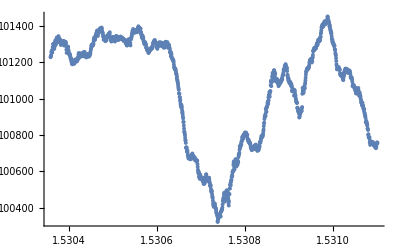

```mathematica
ListPlot[ data[[100;;  ,{1,4}]]]
```

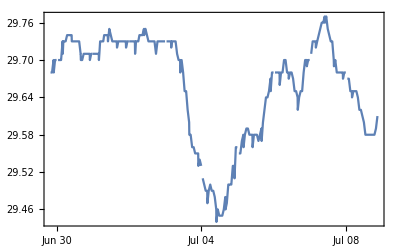

```mathematica
DateListPlot[data2[[6500;;  ,{6,21}]]]
```

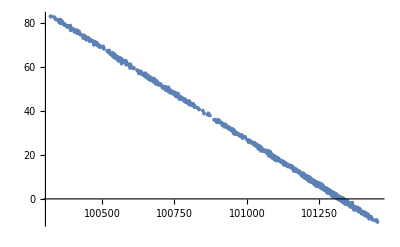

```mathematica
ListPlot[data[[100;;,{4,5}]]]
```

```mathematica
ListPlot3D[data[[10;;,{3,4,5}]]]
```

-Graphics3D-

```mathematica
Hue[0.88]
ColorData["Rainbow"][0.97]
(ColorData["Rainbow"][0.97]&)[1]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
List

[Rescale[#2,{-1,1}]]&)   ColorFunction->Function[{x},(ColorData["Rainbow"][0.97])]

ColorFunction->(ColorData["Rainbow"][0.88]&)

ColorFunctionScaling->False,[Rescale[#3/100000,{0,1}]]
```